105.509

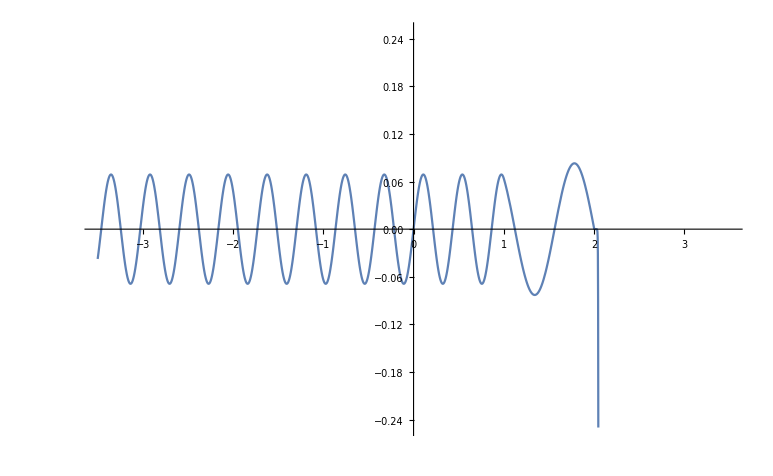

```mathematica
Clear[e,psi]
v[x_]:= Piecewise[{{99999, x<0}, {0, 0<x<1}, {80, 1<x<2}, {99999, 2<x}}]
e=105.50902145
psi=psi/.NDSolve[{
-(1/2)psi''[u]+(v[u]-e)psi[u]==0,
psi[0]==0,
psi'[0]==1
},psi,{u,-3.5,3.5}][[1]];
Plot[psi[u],{u,-3.5,3.5}, PlotRange->{-.25, .25}]
```

```mathematica
psi[2.1]
```

5.65851×10^10